## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_}]:=Module[{gridLabel,gridData},
gridLabel={"k","(X^k)","f(X^k)","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
gridData[[All,4]]=SetAccuracy[norms,4];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,setX_,setY_,{points_,fValues_}]:=Module[{},
ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
Antigrad[point_, func_] := -Grad[func[{x, y}], {x, y}] /. {x->point[[1]],y->point[[2]]};
```

## Алгоритм

```mathematica
Algorithm[{x0_, y0_},func_,ϵ_, method_] := Module [
{
X = {{x0, y0}},
y = {},
w= {},
norms = {},
A = IdentityMatrix[2],
dA = {},
dX = {},
dw = {},
p = 0,
κ = 0,
restart = 0
},

y ={ func[Last@X] };
p = Antigrad[Last@X, func];
w = {p};
norms = {Norm[Last@w]};
While[Last@norms ≥ ϵ,
κ = NArgMin[func[Last@X + α * p], α];
dX = κ * p;
AppendTo[X, Last@X + dX ];
AppendTo[y, func[Last@X]];
AppendTo[w, Antigrad[Last@X, func]];
AppendTo[norms, Norm@Last@w];
dw = w[[-1]] - w[[-2]];
dA =method[A, dX, dw];
If[restart>5, A = IdentityMatrix[2]; restart = 0;, A += dA; ++restart;];
p = A.Last@w;
] ;
{X, y, norms}
];
```

## Методы вычисления ΔA

```mathematica
DavidFletcherPauell[A_,dX_, dw_] :=-KroneckerProduct[dX, dX]/(dw.dX)-KroneckerProduct[A.dw, A.dw]/((A.dw).dw);
BroidenPauellGoldfarbShenno[A_,dX_, dw_] := DavidFletcherPauell[A, dX, dw] -(A.dw).dw * KroneckerProduct[(A.dw)/((A.dw).dw)-dX/(dw.dX), (A.dw)/((A.dw).dw)-dX/(dw.dX)];
Pauell[A_,dX_, dw_]  := -KroneckerProduct[dX + A.dw, dX + A.dw]/(dw.(dX + A.dw));
McKormick[A_,dX_, dw_]:=- KroneckerProduct[dX,dX]/(dw.dX)+ KroneckerProduct[A.dw, dX]/(dX.dw);
```

```mathematica
a = IdentityMatrix[2]; dx = {1, 1}; dw = Antigrad[dx, f];
```

## Функции:

```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
g[{x_,y_}]:=8 x^2+5 y^2-4x y + 8 √5(x+2y)+64;
rosenbrok[{x_,y_}]:=(1-x)^2+(y-x^2)^2;
```

## Вычисления:

```mathematica
(*DavidFletcherPauell
BroidenPauellGoldfarbShenno
Pauell
McKormick*)
```

### Первый пример:

```mathematica
func =g;(*x0 = {√5,0}, x1 = {0 , 2 √5}*)
method = Pauell;
Res = Algorithm[{0,2 √5}, func, 0.001, method];
X = Res[[1]];
Y = Res[[2]];
norms = Res[[3]];
setX = {x,-7,7};
setY ={y,-7,7};
```

### Второй пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
method = McKormick;
Res = Algorithm[{-1,-2}, func, 0.001, method];
X = Res[[1]];
Y = Res[[2]];
norms = Res[[3]];
setX = {x,-7,7};
setY ={y,-7,7};
```

## Результаты:

-Graphics-

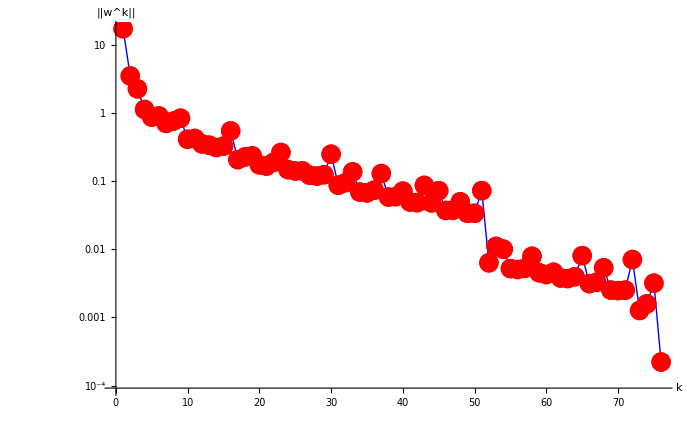

k | (X^k) | f(X^k) | ||w^k||
0 | ( -1.000, -2.000 ) | 13. | 17.09
1 | ( 0.379, -1.483 ) | 3.031 | 3.474
2 | ( -0.030, -0.394 ) | 1.216 | 2.25
3 | ( 0.550, -0.239 ) | 0.496 | 1.121
4 | ( 0.431, -0.123 ) | 0.419 | 0.864
5 | ( 0.596, -0.079 ) | 0.352 | 0.9
6 | ( 0.522, -0.046 ) | 0.33 | 0.7
7 | ( 0.579, -0.043 ) | 0.321 | 0.757
8 | ( 0.564, 0.301 ) | 0.19 | 0.833
9 | ( 0.715, 0.307 ) | 0.123 | 0.41
10 | ( 0.683, 0.372 ) | 0.109 | 0.421
11 | ( 0.740, 0.372 ) | 0.099 | 0.351
12 | ( 0.715, 0.399 ) | 0.094 | 0.335
13 | ( 0.733, 0.392 ) | 0.092 | 0.31
14 | ( 0.720, 0.406 ) | 0.091 | 0.325
15 | ( 0.856, 0.537 ) | 0.059 | 0.544
16 | ( 0.810, 0.584 ) | 0.041 | 0.206
17 | ( 0.837, 0.589 ) | 0.039 | 0.226
18 | ( 0.821, 0.630 ) | 0.034 | 0.234
19 | ( 0.844, 0.627 ) | 0.032 | 0.173
20 | ( 0.839, 0.631 ) | 0.031 | 0.166
21 | ( 0.852, 0.632 ) | 0.031 | 0.188
22 | ( 0.844, 0.697 ) | 0.025 | 0.262
23 | ( 0.880, 0.702 ) | 0.02 | 0.147
24 | ( 0.870, 0.715 ) | 0.019 | 0.14
25 | ( 0.887, 0.717 ) | 0.018 | 0.141
26 | ( 0.878, 0.724 ) | 0.017 | 0.122
27 | ( 0.883, 0.723 ) | 0.017 | 0.118
28 | ( 0.879, 0.727 ) | 0.017 | 0.124
29 | ( 0.932, 0.783 ) | 0.012 | 0.248
30 | ( 0.913, 0.801 ) | 0.009 | 0.087
31 | ( 0.922, 0.803 ) | 0.008 | 0.095
32 | ( 0.918, 0.835 ) | 0.007 | 0.136
33 | ( 0.931, 0.833 ) | 0.006 | 0.069
34 | ( 0.929, 0.833 ) | 0.006 | 0.067
35 | ( 0.927, 0.836 ) | 0.006 | 0.073
36 | ( 0.951, 0.857 ) | 0.005 | 0.129
37 | ( 0.942, 0.868 ) | 0.004 | 0.058
38 | ( 0.947, 0.868 ) | 0.004 | 0.059
39 | ( 0.944, 0.878 ) | 0.003 | 0.071
40 | ( 0.950, 0.877 ) | 0.003 | 0.049
41 | ( 0.948, 0.878 ) | 0.003 | 0.048
42 | ( 0.960, 0.887 ) | 0.003 | 0.086
43 | ( 0.953, 0.895 ) | 0.002 | 0.048
44 | ( 0.966, 0.904 ) | 0.002 | 0.072
45 | ( 0.961, 0.908 ) | 0.002 | 0.037
46 | ( 0.963, 0.908 ) | 0.002 | 0.037
47 | ( 0.961, 0.914 ) | 0.002 | 0.05
48 | ( 0.964, 0.913 ) | 0.002 | 0.034
49 | ( 0.963, 0.913 ) | 0.002 | 0.034
50 | ( 0.999, 0.980 ) | 0.0003 | 0.072
51 | ( 0.993, 0.983 ) | 0. | 0.006
52 | ( 0.994, 0.984 ) | 0. | 0.011
53 | ( 0.994, 0.987 ) | 0. | 0.01
54 | ( 0.995, 0.987 ) | 0. | 0.005
55 | ( 0.995, 0.988 ) | 0. | 0.005
56 | ( 0.995, 0.988 ) | 0. | 0.005
57 | ( 0.995, 0.989 ) | 0. | 0.008
58 | ( 0.996, 0.990 ) | 0. | 0.005
59 | ( 0.996, 0.990 ) | 0. | 0.004
60 | ( 0.996, 0.990 ) | 0. | 0.005
61 | ( 0.996, 0.990 ) | 0. | 0.004
62 | ( 0.996, 0.990 ) | 0. | 0.004
63 | ( 0.996, 0.990 ) | 0. | 0.004
64 | ( 0.997, 0.992 ) | 0. | 0.008
65 | ( 0.997, 0.992 ) | 0. | 0.003
66 | ( 0.997, 0.992 ) | 0. | 0.003
67 | ( 0.997, 0.993 ) | 0. | 0.005
68 | ( 0.997, 0.993 ) | 0. | 0.003
69 | ( 0.997, 0.993 ) | 0. | 0.002
70 | ( 0.997, 0.993 ) | 0. | 0.003
71 | ( 0.999, 0.996 ) | 0. | 0.007
72 | ( 0.999, 0.997 ) | 0. | 0.001
73 | ( 0.999, 0.997 ) | 0. | 0.002
74 | ( 1.000, 0.999 ) | 0. | 0.003
75 | ( 1.00, 0.999 ) | 0. | 0.0002

```mathematica
PlotMethod[func,setX,setY,{X, Y}]
PlotNorms[norms]
MakeTable[Res]
```